2.95109

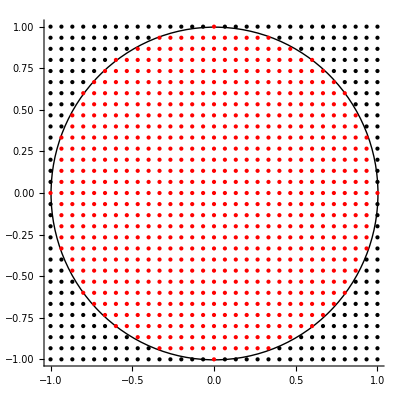

3.13778

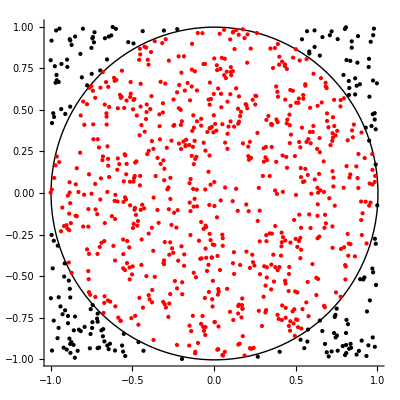

{0.15625,3.11052}

{0.046875,3.1323}

```mathematica
(*approximate π using points*)
countInCircle[list_] := Count[list, x_/;x.x≤1] (*Note: different (worse!) results if we exclude 1*)
estimateByPoints[list_] := N[4*countInCircle[list]/Length[list]]
uniformGrid[n_]:=Flatten[Table[{x,y},{x,-1,1,2/n},{y,-1,1,2/n}],1]
randomGrid[n_] := Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},n]

unif = uniformGrid[30];
estimateByPoints[unif]//N
Graphics[{Circle[], Table[{If[p.p≤1, Red, Black],Point[p]},{p,unif}]}, Axes-> True]
rand = randomGrid[30*30];
estimateByPoints[rand]//N
Graphics[{Circle[], Table[{If[p.p≤1, Red, Black],Point[p]},{p,rand}]}, Axes-> True]

(*comparison; they both generate around 4 * 10^4 points*)
Timing[estimateByPoints[uniformGrid[200]]]
Timing[estimateByPoints[randomGrid[40000]]]
```

3.08425

3.09965

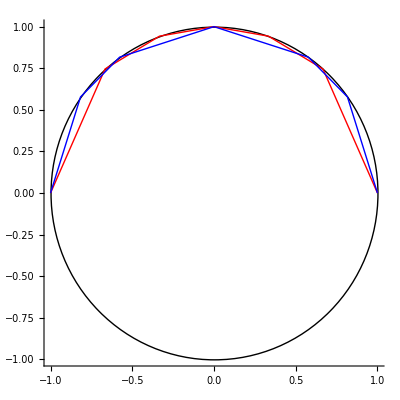

{0.5625,3.14159236}

{0.953125,3.141592446}

```mathematica
(*calculate the length of a piecewise linear curve, given a nonempty list of vertices*)
lineLength[line_]:=Sum[Norm[line[[i+1]]-line[[i]]],{i,1,Length[line]-1}]
circxy[x_] := N[{x,Sqrt[1-x^2]}] (*given x, finds the pair (x,y) on the sphere with y≥0*)
halfcircumference1[n_]:=Table[circxy[x],{x,-1,1,1/n}];
halfcircumference2[n_]:=(*alternate method with more nodes for x closer to +-1*)
Table[circxy[Sqrt[Abs[x]]Sign[x]],{x,-1,1,1/n}];

line1=halfcircumference1[3];
line2=halfcircumference2[3];
lineLength[line1]
lineLength[line2]
Graphics[{Circle[],Red, Line[line1], Blue, Line[line2]}, Axes->True]

Timing[NumberForm[lineLength[halfcircumference1[10000]],10]]
Timing[NumberForm[lineLength[halfcircumference2[10000]],10]]
```

```mathematica
(*from now on we work only on the first quadrant, and we represent rectangles by their lower-left and upper-right corners*)
inCircleQ[rect_]:=rect[[2]].rect[[2]]<1;
outOfCircleQ[rect_] := rect[[1]].rect[[1]]≥1;
groupRectangles[rects_] :=(*returns three lists: those of the rectangles inside the circle, those in the boundary, and those outside*)
Module[{in={},mid={},out={}},
Do[If[inCircleQ[r], AppendTo[in, r],
If[outOfCircleQ[r],AppendTo[out,r],
AppendTo[mid,r]]],
{r,rects}];
{in,mid,out}]
uniformRectangles[n_]:=Flatten[
Table[{{x,y},{x+1/n,y+1/n}},{x,0,1,1/n},{y,0,1,1/n}],1]
area[rect_] := N[(rect[[2,1]]-rect[[1,1]])(rect[[2,2]]-rect[[1,2]])];

(*the following functions assume rectangles are already grouped*)
piFromRectangles[groups_] :=(*returns a list with a lower and upper estimate for π*)
Module[{lower, higher},
lower = Sum[area[r],{r,groups[[1]]}];
higher = lower+Sum[area[r],{r,groups[[2]]}];
{4lower,4higher}]
drawRectangles[groups_] :=
Graphics[{Thick,Circle[],EdgeForm[Thick],
Red, Map[Apply[Rectangle],groups[[1]]],
Transparent, Map[Apply[Rectangle],groups[[2]]],
Opacity[1],Blue,Map[Apply[Rectangle],groups[[3]]]},
Axes->True, PlotRange->{{0,1.2},{0,1.2}}
]
```

{2.44444,3.66667}

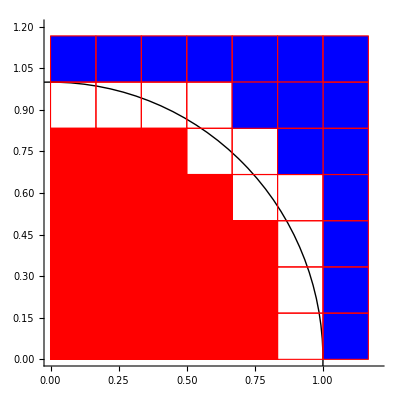

{0.0625,{3.0512,3.2096}}

{0.390625,{3.1,3.1796}}

```mathematica
u6 =uniformRectangles[6];
piFromRectangles[groupRectangles[u6]]
drawRectangles[groupRectangles[u6]]

Timing[piFromRectangles[groupRectangles@uniformRectangles[50]]]
Timing[piFromRectangles[groupRectangles@uniformRectangles[100]]]
```

```mathematica
(*less wasteful algorithm: only splits rectangles that are not entirely inside the circle or outside*)
(*n is the number of iterations, ie it splits into rectangles as small as 2^-n*)

(*aux function to split a rectangle in 4*)
split[{{x1_,y1_},{x2_,y2_}}]:=Module[{xm = (x1+x2)/2, ym = (y1+y2)/2},
Flatten[Table[{{x,y},{x+xm-x1,y+ym-y1}}, {x,{x1,xm}},{y,{y1,ym}}],1]]

betterRectangles[n_]:= Module[{in={}, mid={ {{0,0},{1,1}} }, out={}, splitmid, groups},
Do[
splitmid = Flatten[Map[split,mid],1];
groups = groupRectangles[splitmid];
in = Join[in,groups[[1]]];
out =Join[out,groups[[3]]];
mid=groups[[2]]
,n];
{in,mid,out}]
```

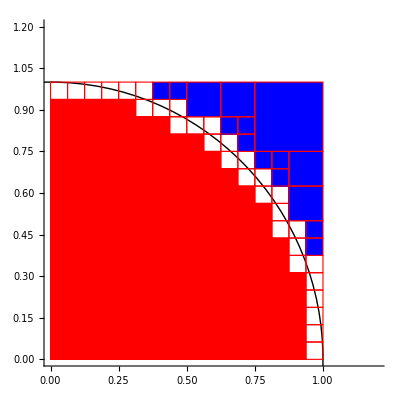

```mathematica
drawRectangles[betterRectangles[4]]
```

```mathematica
Timing[piFromRectangles[betterRectangles[12]]]
```

{1.32813,{3.1406,3.14255}}

0.0159773+0.861085 t+0.286322 t^2-0.401682 t^3+0.0886419 t^4-0.00564312 t^5

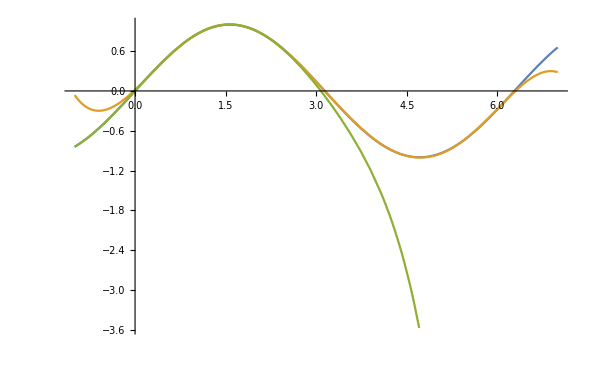

```mathematica
(*exercise 2*)
euc[v_, w_] := v.w
t0 = 0; t1 = 2π;
(*inner product in L2; the arguments are expressions with variable t*)
l2[v_, w_] := Integrate[v w, {t,t0, t1}];

(*the argument "inner" in the following functions is the inner product to be used*)
(*this allows them to work on vectors in Rn, which was useful for testing purposes*)
gramschmidt[list_, inner_] := (*assumes linear independence*)
If[list=={}, {},
Module[{previous = gramschmidt[list[[;;-2]], inner], v = Last[list]},
Append[previous, normalize[v-project[v,previous,inner], inner]]]]
project[v_, on_, inner_]:= (*assumes on is orthonormal list*)
Sum[inner[v,w] w, {w, on}]
normalize[v_, inner_] := v/Sqrt[inner[v,v]]

bp6 = gramschmidt[{1,t,t^2,t^3, t^4,t^5, t^6},l2];
sinapprox =N[project[Sin[t], bp6, l2]]//Simplify
(*compare our approximation (orange), sine (blue), and the taylor expansion up to t^7 (green)*)
Plot[{Sin[t], sinapprox, t-1/6 t^3 + 1/Factorial[5] t^5-1/Factorial[7] t^7},{t,-1,7}]
```

{{0,0},{1,1},{2,0}}

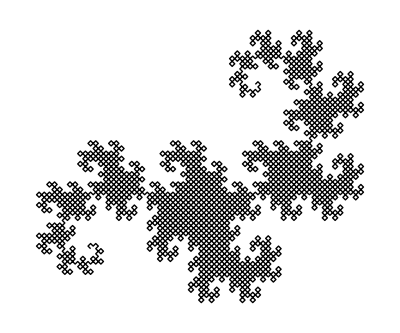

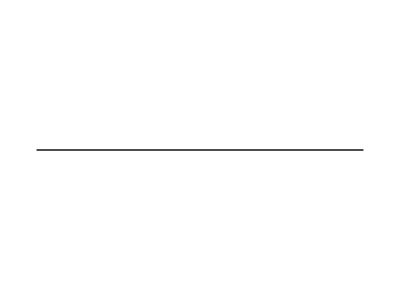
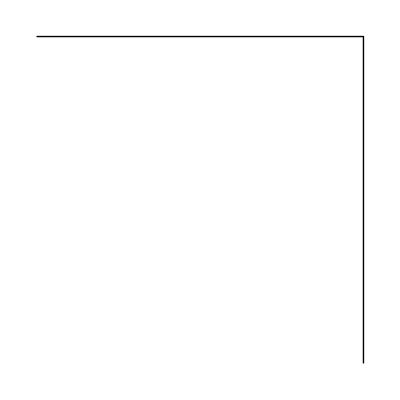
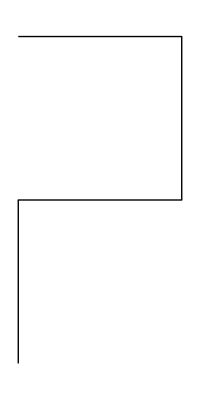
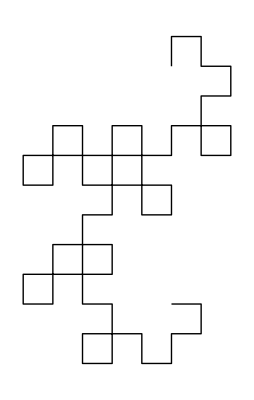
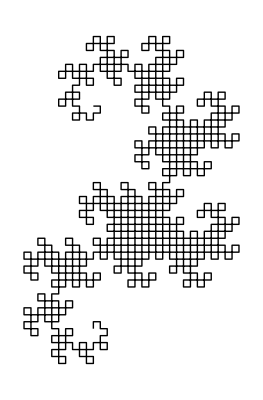
n | 0 | 1 | 2 | 6 | 10
S_n | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

C:\Users\Robly\Desktop\theorems\theorems\ME\dragon.png

C:\Users\Robly\Desktop\theorems\theorems\ME\dragontable.png

```mathematica
dragoniter[list_]:=Module[{midpoint=Last[list]},
Join[list,
Reverse[Table[midpoint +RotationMatrix[π/2].(q-midpoint),{q,list[[;;-2]]}]]]]
dragoniter[{{0,0},{1,1}}]

dragon=Graphics[{Line[Nest[dragoniter,N@{{0,0},{1,1}},12]]}]
dragontable = TableForm[
Transpose@Table[{i,Graphics[{Line[Nest[dragoniter,N@{{0,0},{1,0}},i]]}]},
{i,{0,1,2,6,10}}],
TableHeadings->{{"n","S_n"},None}]
Export[NotebookDirectory[]~StringJoin~"dragon.png",dragon]
Export[NotebookDirectory[]~StringJoin~"dragontable.png",dragontable]
```

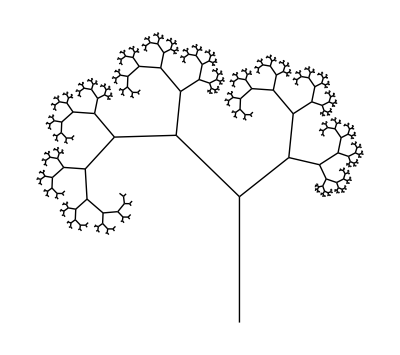

```mathematica
iteratetree[transforms_][ list_]:=(*transformations are given by complex numbers*)
Flatten[Table[Map[Map[tr#+I&], list], {tr,transforms}], 1]//Append[{0,I}]
Graphics[Map[Line]@Map[ReIm]@Nest[iteratetree[{.7Exp[.8I],.5Exp[-.9I]}],{},10]]
```

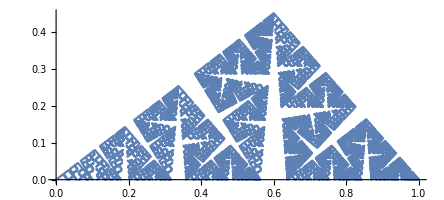

```mathematica
kochpeanoiter[a_][list_]:=Join[Map[a Conjugate[#]&,list[[;;-2]]],Map[a+(1-a)Conjugate[#]&,list]];
ComplexListPlot[Nest[kochpeanoiter[.6+.45I],{0,1},13],Joined->True]
```

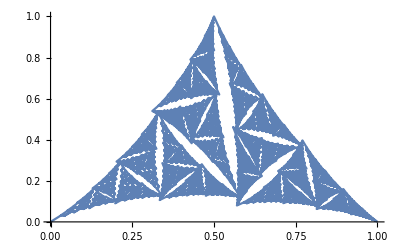

```mathematica
derhamiter[a_,b_,c_,d_,e_,f_][list_]:=Join[Map[({{a, c}, {b, d}}).#&,list[[;;-2]]],Map[({{1-a, e}, {-b, f}}).# + {a,b}&,list]];
ListPlot[Nest[derhamiter[.5,1.,.33,-.38,-.18,-.42],{{0,0},{1,0}},13],Joined->True]
```

```mathematica
bfern[transf_,weights_,n_]:= (*applies trans[[i]] with probability weights[[i]]/Total[weights]*)
Module[{iterate={0,0},output},
output={iterate};
Do[iterate=RandomChoice[weights->transf][iterate]; AppendTo[output,iterate],n];
output]
```

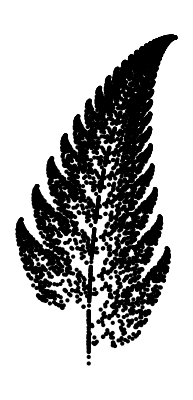

```mathematica
f1[{x_,y_}]:={0,.16y};
f2[{x_,y_}]:={.85x+.04y,-.04x+.85y+1.6};
f3[{x_,y_}]:={.2x-.26y,.23x+.22y+1.6};
f4[{x_,y_}]:={-.15x+.28y,.26x+.24y+.44};
fern = bfern[{f1,f2,f3,f4},{1,85,7,7},6000];
Graphics[Map[Point,fern]]
```